2.22165 x

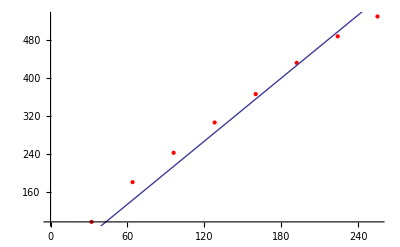

2.13055 x

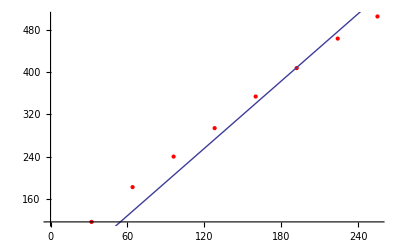

```mathematica
voltages={32,64,96,128,160,192,224,255};
rFreq={{32,96},{64,180},{96,242},{128,306},{160,366},{192,432},{224,488},{255,530}};
lFreq={{32,116},{64,182},{96,240},{128,294},{160,354},{192,408},{224,464},{255,506}};
rf=Fit[rFreq, {x},x];
rf
Show[ListPlot[rFreq,PlotStyle->Red],Plot[rf,{x,0,255}]]
lf=Fit[lFreq, {x},x];
lf
Show[ListPlot[lFreq,PlotStyle->Red],Plot[lf,{x,0,255}]]
```